```mathematica
S[x_]:=4/(Sqrt[Pi W])Exp[-x^2/W]
Subscript[k, w][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}]
Subscript[k, l][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}]
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1,Subscript[L, 1]->1}];
```

```mathematica
Subscript[T, -2][ξ_]:=Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ<Subscript[A, 0]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]]+
Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[A, 0]},Assumptions->{ξ<Subscript[A, 0],W>0}]
Subscript[H, -2][ξ_]=Refine[Subscript[T, -2][ξ]/.var,ξ<Subscript[A, 0]<0];
Subscript[T, -1][ξ_]:=Limit[Subscript[c, 2] Subscript[k, w][x,ξ]-Subscript[c, 1] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ<Subscript[L, 0]]-
		Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+ D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ>Subscript[A, 0]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0],Subscript[A, 0]<Subscript[L, 0]}/.var]+
Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0],Subscript[A, 0]<Subscript[L, 0],W>0}/.var]
Subscript[H, -1][ξ_]=Refine[Subscript[T, -1][ξ]/.var,{Subscript[A, 0]<ξ<Subscript[L, 0]}/.var];
Subscript[T, 1][ξ_]:=Limit[Subscript[c, 5] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 1],Assumptions->ξ<Subscript[A, 1]]-
		Limit[Subscript[c, 4] Subscript[k, w][x,ξ]-Subscript[c, 3] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ>Subscript[L, 1]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[L, 1],Subscript[A, 1]}/.var,Assumptions->{Subscript[L, 1]<ξ<Subscript[A, 1],Subscript[L, 1]<Subscript[A, 1]}/.var]+
Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[L, 1],Subscript[A, 1]}/.var,Assumptions->{Subscript[L, 1]<ξ<Subscript[A, 1],Subscript[L, 1]<Subscript[A, 1],W>0}/.var]
Subscript[H, 1][ξ_]=Refine[Subscript[T, 1][ξ]/.var,{Subscript[L, 1]<ξ<Subscript[A, 1]}/.var];
Subscript[T, 2][ξ_]:=-Limit[Subscript[c, 5] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 1],Assumptions->ξ>Subscript[A, 1]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 1],∞},Assumptions->ξ>Subscript[A, 1]]+
Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 1],∞},Assumptions->{ξ>Subscript[A, 1],W>0}]
Subscript[H, 2][ξ_]=Refine[Subscript[T, 2][ξ]/.var,0<Subscript[A, 1]<ξ];
```

```mathematica
Gen[ξ_]:=Limit[Subscript[G, 1] Subscript[k, l][x,ξ]-Subscript[G, 2] D[Subscript[k, l][x,ξ], x],x->Subscript[G, 3],Assumptions->ξ<Subscript[G, 3]]-
		Limit[Subscript[G, -1] Subscript[k, l][x,ξ]-Subscript[G, -2] D[Subscript[k, l][x,ξ], x],x->Subscript[G, -3],Assumptions->ξ>Subscript[G, -3]]-
Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[G, -3],Subscript[G, 3]},Assumptions->Subscript[G, -3]<0<Subscript[G, 3]]+
Subscript[η, l](1-Subscript[G, 0])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[G, -3],Subscript[G, 3]},Assumptions->{Subscript[G, -3]<0<Subscript[G, 3],W>0}];
G[ξ_]=Refine[Gen[ξ]/.var,{Subscript[G, -3]<ξ<Subscript[G, 3]}];
```

```mathematica
(* Begin n-formulations *)
n=1000;
f=1;
Subscript[F, 0][ξ_]=G[ξ]/.{Subscript[G, 0]->Subscript[a, f],Subscript[G, -1]->Subscript[d, -1],Subscript[G, 1]->Subscript[d, 1],Subscript[G, -2]->Subscript[g, -1],Subscript[G, 2]->Subscript[g, 1],Subscript[G, -3]->Subscript[B, -1],Subscript[G, 3]->Subscript[B, 1]}/.var;
For[i=1,i<=n,i++,
Subscript[F, i][ξ_]=G[ξ]/.{Subscript[G, 0]->Subscript[a, Mod[i+f,2]],Subscript[G, -1]->Subscript[d, i],Subscript[G, 1]->Subscript[d, i+1],Subscript[G, -2]->Subscript[g, i],Subscript[G, 2]->Subscript[g, i+1],Subscript[G, -3]->Subscript[B, i],Subscript[G, 3]->Subscript[B, i+1]}/.var;
Subscript[F, -i][ξ_]=G[ξ]/.{Subscript[G, 0]->Subscript[a, Mod[i+f,2]],Subscript[G, -1]->Subscript[d, -i-1],Subscript[G, 1]->Subscript[d, -i],Subscript[G, -2]->Subscript[g, -i-1],Subscript[G, 2]->Subscript[g, -i],Subscript[G, -3]->Subscript[B, -i-1],Subscript[G, 3]->Subscript[B, -i]}/.var;
]
corr={Subscript[B, n+1]->Subscript[L, 1],Subscript[d, n+1]->M Subscript[c, 4],Subscript[g, n+1]->Subscript[c, 3],Subscript[B, -n-1]->Subscript[L, 0],Subscript[d, -n-1]->M Subscript[c, 2],Subscript[g, -n-1]->Subscript[c, 1]}/.var;
For[i=-n,i<=n,i++,corr=Join[corr,{Subscript[g, i]->0}]]
For[i=-n,i<=n,i++,Subscript[F, i][ξ_]=Subscript[F, i][ξ]/.corr]
```

```mathematica
Subscript[eqn, 1]=Subscript[H, -2][Subscript[A, 0]]+1==0;
Subscript[eqn, 2]=Subscript[H, -1][Subscript[A, 0]]+1==0;
Subscript[eqn, 3]=Subscript[H, 1][Subscript[A, 1]]+1==0;
Subscript[eqn, 4]=Subscript[H, 2][Subscript[A, 1]]+1==0;
Subscript[eqn, 5]=Subscript[F, -n]'[Subscript[L, 0]]-M Subscript[H, -1]'[Subscript[L, 0]]==0/.var;
Subscript[eqn, 6]=Subscript[F, n]'[Subscript[L, 1]]-M Subscript[H, 1]'[Subscript[L, 1]]==0/.var;
Subscript[eqn, 7]=Subscript[F, -n][Subscript[L, 0]]-Subscript[H, -1][Subscript[L, 0]]==0/.var;
Subscript[eqn, 8]=Subscript[F, n][Subscript[L, 1]]-Subscript[H, 1][Subscript[L, 1]]==0/.var;

eqns={Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7],Subscript[eqn, 8]};

For[i=-n,i<=n,i++,
	If[i==-n,eqns=Join[eqns,{Subscript[F, -n][Subscript[B, -n]]==0}],Nothing];
	If[i==n,eqns=Join[eqns,{Subscript[F, n][Subscript[B, n]]==0}],Nothing];
	If[i==0,eqns=Join[eqns,{Subscript[F, 0][Subscript[B, 1]]==0,Subscript[F, 0][Subscript[B, -1]]==0}],Nothing];
	If[-n<i<0,eqns=Join[eqns,{Subscript[F, i][Subscript[B, i]]==0,Subscript[F, i][Subscript[B, i-1]]==0}],Nothing];
	If[0<i<n,eqns=Join[eqns,{Subscript[F, i][Subscript[B, i]]==0,Subscript[F, i][Subscript[B, i+1]]==0}],Nothing];
]
variables={{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[c, 5],0},{Subscript[A, 0],-1.5},{Subscript[A, 1],1.5}};
For[i=-n,i<=n,i++,If[i==0,Nothing,variables=Join[variables,{{Subscript[B, i],N[i/(n+1)]},{Subscript[d, i],0}}]]]
```

```mathematica
(*Creating all n-boundary solutions up to m*)
m=20;

For[l=1,l<m,l++,
(* Making new boundary formulations *)
n=l;
f=1;
Subscript[F, 0][ξ_]=G[ξ]/.{Subscript[G, 0]->Subscript[a, f],Subscript[G, -1]->Subscript[d, -1],Subscript[G, 1]->Subscript[d, 1],Subscript[G, -2]->Subscript[g, -1],Subscript[G, 2]->Subscript[g, 1],Subscript[G, -3]->Subscript[B, -1],Subscript[G, 3]->Subscript[B, 1]}/.var;
For[i=1,i<=n,i++,
Subscript[F, i][ξ_]=G[ξ]/.{Subscript[G, 0]->Subscript[a, Mod[i+f,2]],Subscript[G, -1]->Subscript[d, i],Subscript[G, 1]->Subscript[d, i+1],Subscript[G, -2]->Subscript[g, i],Subscript[G, 2]->Subscript[g, i+1],Subscript[G, -3]->Subscript[B, i],Subscript[G, 3]->Subscript[B, i+1]}/.var;
Subscript[F, -i][ξ_]=G[ξ]/.{Subscript[G, 0]->Subscript[a, Mod[i+f,2]],Subscript[G, -1]->Subscript[d, -i-1],Subscript[G, 1]->Subscript[d, -i],Subscript[G, -2]->Subscript[g, -i-1],Subscript[G, 2]->Subscript[g, -i],Subscript[G, -3]->Subscript[B, -i-1],Subscript[G, 3]->Subscript[B, -i]}/.var;
];
corr={Subscript[B, n+1]->Subscript[L, 1],Subscript[d, n+1]->M Subscript[c, 4],Subscript[g, n+1]->Subscript[c, 3],Subscript[B, -n-1]->Subscript[L, 0],Subscript[d, -n-1]->M Subscript[c, 2],Subscript[g, -n-1]->Subscript[c, 1]}/.var;
For[i=-n,i<=n,i++,corr=Join[corr,{Subscript[g, i]->0}]];
For[i=-n,i<=n,i++,Subscript[F, i][ξ_]=Subscript[F, i][ξ]/.corr];


(* Making equations to solve for the unknowns *)
Subscript[eqn, 1]=Subscript[H, -2][Subscript[A, 0]]+1==0;
Subscript[eqn, 2]=Subscript[H, -1][Subscript[A, 0]]+1==0;
Subscript[eqn, 3]=Subscript[H, 1][Subscript[A, 1]]+1==0;
Subscript[eqn, 4]=Subscript[H, 2][Subscript[A, 1]]+1==0;
Subscript[eqn, 5]=Subscript[F, -n]'[Subscript[L, 0]]-M Subscript[H, -1]'[Subscript[L, 0]]==0/.var;
Subscript[eqn, 6]=Subscript[F, n]'[Subscript[L, 1]]-M Subscript[H, 1]'[Subscript[L, 1]]==0/.var;
Subscript[eqn, 7]=Subscript[F, -n][Subscript[L, 0]]-Subscript[H, -1][Subscript[L, 0]]==0/.var;
Subscript[eqn, 8]=Subscript[F, n][Subscript[L, 1]]-Subscript[H, 1][Subscript[L, 1]]==0/.var;

eqns={Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7],Subscript[eqn, 8]};

For[i=-n,i<=n,i++,
	If[i==-n,eqns=Join[eqns,{Subscript[F, -n][Subscript[B, -n]]==0}],Nothing];
	If[i==n,eqns=Join[eqns,{Subscript[F, n][Subscript[B, n]]==0}],Nothing];
	If[i==0,eqns=Join[eqns,{Subscript[F, 0][Subscript[B, 1]]==0,Subscript[F, 0][Subscript[B, -1]]==0}],Nothing];
	If[-n<i<0,eqns=Join[eqns,{Subscript[F, i][Subscript[B, i]]==0,Subscript[F, i][Subscript[B, i-1]]==0}],Nothing];
	If[0<i<n,eqns=Join[eqns,{Subscript[F, i][Subscript[B, i]]==0,Subscript[F, i][Subscript[B, i+1]]==0}],Nothing];
];
variables={{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[c, 5],0},{Subscript[A, 0],-1.5},{Subscript[A, 1],1.5}};
For[i=-n,i<=n,i++,If[i==0,Nothing,variables=Join[variables,{{Subscript[B, i],N[i/(n+1)]},{Subscript[d, i],0}}]]];

(* Starting at midpoint and iterating to the sides to find solution domain *)
Subscript[Q, mid]=479.63303010174509905667606433480288977587`30.;
step=0.5`30.;
sols={};
loop=True;
Monitor[
For[i=0,loop,i++,
tempQ={Q->Subscript[Q, mid]+i step,W->6};
sol=Quiet[FindRoot[eqns/.tempQ,variables,MaxIterations->1000,WorkingPrecision->30]];
sol=Join[sol,tempQ,var/.tempQ];
Quiet[conds=Subscript[H, 1][Subscript[L, 1]](-1)^(1+f+l)>0/.sol];
If[conds,funcList={{Subscript[H, 2][-x],x<Subscript[A, 0]},{Subscript[H, -1][x],Subscript[A, 0]<=x<Subscript[L, 0]},{Subscript[H, 1][x],Subscript[L, 1]<x<=Subscript[A, 1]},{Subscript[H, 2][x],Subscript[A, 1]<x}};
For[j=-n,j<=n,j++,
	If[j==-n,funcList=Join[funcList,{{Subscript[F, -n][x],Subscript[L, 0]<=x<Subscript[B, -n]}}],Nothing];
	If[j==n,funcList=Join[funcList,{{Subscript[F, n][x],Subscript[B, n]<x<=Subscript[L, 1]}}],Nothing];
	If[j==0,funcList=Join[funcList,{{Subscript[F, 0][x],Subscript[B, -1]<x<Subscript[B, 1]}}],Nothing];
	If[-n<j<0,funcList=Join[funcList,{{Subscript[F, j][x],Subscript[B, j-1]<x<Subscript[B, j]}}],Nothing];
	If[0<j<n,funcList=Join[funcList,{{Subscript[F, j][x],Subscript[B, j]<x<Subscript[B, j+1]}}],Nothing];];
M[x_]=Piecewise[funcList/.sol];
NUM=12001;
points=SetPrecision[Table[-6+12(i-1)/(NUM-1),{i,NUM}],20];
nSolution=N[Map[M, points]];
sols=Join[sols,{{N[Q/.sol],N[M[0]/.sol],nSolution}}],loop=False];
],{N[Q/.tempQ],N[l/(m-1)]}];
loop=True;
Monitor[
For[i=0,loop,i++,
tempQ={Q->Subscript[Q, mid]-i step,W->6};
sol=Quiet[FindRoot[eqns/.tempQ,variables,MaxIterations->1000,WorkingPrecision->30]];
sol=Join[sol,tempQ,var/.tempQ];
Quiet[conds=Subscript[H, 1][Subscript[L, 1]](-1)^(1+f+l)>0/.sol];
If[conds,funcList={{Subscript[H, 2][-x],x<Subscript[A, 0]},{Subscript[H, -1][x],Subscript[A, 0]<=x<Subscript[L, 0]},{Subscript[H, 1][x],Subscript[L, 1]<x<=Subscript[A, 1]},{Subscript[H, 2][x],Subscript[A, 1]<x}};
For[j=-n,j<=n,j++,
	If[j==-n,funcList=Join[funcList,{{Subscript[F, -n][x],Subscript[L, 0]<=x<Subscript[B, -n]}}],Nothing];
	If[j==n,funcList=Join[funcList,{{Subscript[F, n][x],Subscript[B, n]<x<=Subscript[L, 1]}}],Nothing];
	If[j==0,funcList=Join[funcList,{{Subscript[F, 0][x],Subscript[B, -1]<x<Subscript[B, 1]}}],Nothing];
	If[-n<j<0,funcList=Join[funcList,{{Subscript[F, j][x],Subscript[B, j-1]<x<Subscript[B, j]}}],Nothing];
	If[0<j<n,funcList=Join[funcList,{{Subscript[F, j][x],Subscript[B, j]<x<Subscript[B, j+1]}}],Nothing];];
M[x_]=Piecewise[funcList/.sol];
NUM=12001;
points=SetPrecision[Table[-6+12(i-1)/(NUM-1),{i,NUM}],20];
nSolution=N[Map[M, points]];
sols=Join[sols,{{N[Q/.sol],N[M[0]/.sol],nSolution}}],loop=False];
],{N[Q/.tempQ],N[l/(m-1)]}];
outputName=StringJoin["C:\\masterA GitHub\\Code\\Gaussian\\Std 6\\3A - IceWater_Snow_WaterIce_u_",ToString[l],".csv"];
Export[outputName,sols,Format->Table];
]
```

```mathematica
Beep[]
```

```mathematica
(*Finding what Q's has solution on this form*)
Subscript[Q, min]=440;
Subscript[Q, max]=520;
m=2(Subscript[Q, max]-Subscript[Q, min])+1;
(*n=1401;*)
Subscript[W, test]=5.2;
sols={};
Monitor[
For[i=0,i<m,i++,
tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(m-1),0],W->Rationalize[Subscript[W, test],0]};
sol=Quiet[FindRoot[eqns/.tempQ,variables,MaxIterations->1000,WorkingPrecision->50]];
sol=Join[sol,tempQ,var/.tempQ];
Quiet[conds=Subscript[A, 0]<Subscript[L, 0]<Subscript[B, -4]<Subscript[B, -3]<Subscript[B, -2]<Subscript[B, -1]<Subscript[B, 1]<Subscript[B, 2]<Subscript[B, 3]<Subscript[B, 4]<Subscript[L, 1]<Subscript[A, 1]&&Subscript[H, 1][Subscript[L, 1]]>0/.sol];
If[conds,funcList={{Subscript[H, 2][-x],x<Subscript[A, 0]},{Subscript[H, -1][x],Subscript[A, 0]<=x<Subscript[L, 0]},{Subscript[H, 1][x],Subscript[L, 1]<x<=Subscript[A, 1]},{Subscript[H, 2][x],Subscript[A, 1]<x}};
For[j=-n,j<=n,j++,
	If[j==-n,funcList=Join[funcList,{{Subscript[F, -n][x],Subscript[L, 0]<=x<Subscript[B, -n]}}],Nothing];
	If[j==n,funcList=Join[funcList,{{Subscript[F, n][x],Subscript[B, n]<x<=Subscript[L, 1]}}],Nothing];
	If[j==0,funcList=Join[funcList,{{Subscript[F, 0][x],Subscript[B, -1]<x<Subscript[B, 1]}}],Nothing];
	If[-n<j<0,funcList=Join[funcList,{{Subscript[F, j][x],Subscript[B, j-1]<x<Subscript[B, j]}}],Nothing];
	If[0<j<n,funcList=Join[funcList,{{Subscript[F, j][x],Subscript[B, j]<x<Subscript[B, j+1]}}],Nothing];];
M[x_]=Piecewise[funcList/.sol];
points=Table[-10+0.01(k-1),{k,2001}];
nSolution=N[Round[Map[M, points],10^-10]];sols=Join[sols,{{N[Round[Q/.sol,10^-10]],N[Round[M[0]/.sol,10^-10]],N[Round[M[0]/.sol,10^-10]],N[Round[M[0]/.sol,10^-10]],nSolution}}],Nothing];
],{N[i/m],N[Q/.tempQ]}]
```

```mathematica
Export["/home/ask/Documents/masterA/Code/Big Project/G 5.2/3A - IceWaterSnowLandSnowWaterIce.csv",sols,Format->Table];
```

True

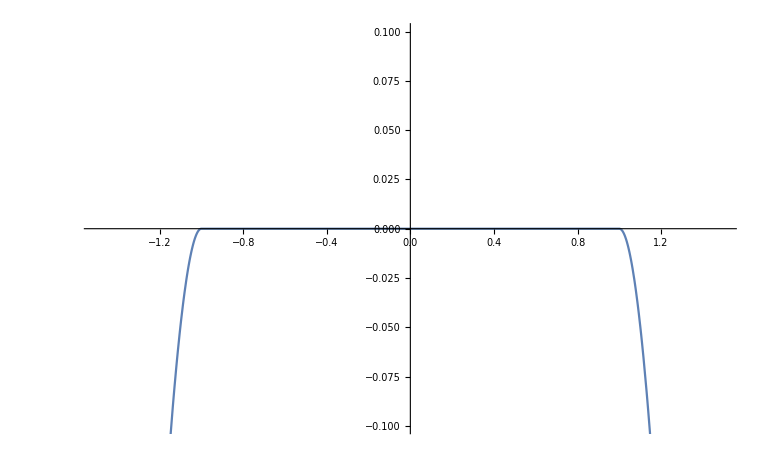

```mathematica
tempQ={Q->Rationalize[479.6330301017451,0],W->6};
sol=FindRoot[eqns/.tempQ,variables,WorkingPrecision->30];
sol=Join[sol,tempQ,var];
funcList={{Subscript[H, 2][-x],x<Subscript[A, 0]},{Subscript[H, -1][x],Subscript[A, 0]<=x<Subscript[L, 0]},{Subscript[H, 1][x],Subscript[L, 1]<x<=Subscript[A, 1]},{Subscript[H, 2][x],Subscript[A, 1]<x}};
For[i=-n,i<=n,i++,
	If[i==-n,funcList=Join[funcList,{{Subscript[F, -n][x],Subscript[L, 0]<=x<Subscript[B, -n]}}],Nothing];
	If[i==n,funcList=Join[funcList,{{Subscript[F, n][x],Subscript[B, n]<x<=Subscript[L, 1]}}],Nothing];
	If[i==0,funcList=Join[funcList,{{Subscript[F, 0][x],Subscript[B, -1]<x<Subscript[B, 1]}}],Nothing];
	If[-n<i<0,funcList=Join[funcList,{{Subscript[F, i][x],Subscript[B, i-1]<x<Subscript[B, i]}}],Nothing];
	If[0<i<n,funcList=Join[funcList,{{Subscript[F, i][x],Subscript[B, i]<x<Subscript[B, i+1]}}],Nothing];
];
M[x_]=Piecewise[funcList/.sol];
Subscript[p, 1]=Plot[M[x],{x,-1.5,1.5}];
Subscript[A, 0]<Subscript[L, 0]<Subscript[B, -1]<Subscript[B, 1]<Subscript[L, 1]<Subscript[A, 1]/.sol
Show[Subscript[p, 1],PlotRange->{{-1.5,1.5},{-0.1,0.1}}]
```

```mathematica
sol
```

{c_0→4.11801674485621808547983782416,c_1→2.19128804928594782271715546606×10^-7,c_2→5.70305132493204173687400776806×10^-7,c_3→2.19128804928594782042944956789×10^-7,c_4→-5.70305132493204173092759767699×10^-7,c_5→-4.11801674485621808547983765425,A_0→-1.4781780326887036206710819128,A_1→1.47817803268870362067108187866,B_-1000→-0.999543323132852736710273572993,d_-1000→-0.000959923608876324800493257571607,B_-999→-0.998690375202274307120920088514,d_-999→0.000959603829184850535246387532306,B_-998→-0.997779886397462097000288651973,d_-998→-0.00096016828609641824459656661419,B_-997→-0.996924954806618396527958755851,d_-997→0.00095984739629907795284189168978,B_-996→-0.996017337235676382383422635486,d_-996→-0.000960407636062323783643073124393,B_-995→-0.99516042150007556031280672662,d_-995→0.000960085636558136167758104722518,3982,B_998→0.997779886397462097001444755377,d_998→0.000960168286096418244095864734733,B_999→0.9986903752022743071216031587,d_999→-0.000959603829184850534746274976928,B_1000→0.999543323132852736710511580403,d_1000→0.000959923608876324799992809533411,Q→1701212313/3546904,W→6,α_w→2529/50,β_w→385/38,η_w→(5 Q)/19,α_l→1922/189,β_l→55/27,η_l→(10 Q)/189,a_0→3/5,a_1→19/50,M→38/189,L_0→-1,L_1→1}
 |  |  |  |

```mathematica
0.0019204097377370428244343503161990484438618062456628829569`30. (*n=500*)
```

```mathematica
0.0009599236088763248004932575716068338655956381400388943817`30. (*n=1000*)
```